# 10.4 Homework

## Problem 4:

```mathematica
(*Find the area of the region enclosed by one loop of the curve.*)
```

```mathematica
F[θ_]:=√(8Cos[2θ]);
G[θ_]=2;
(*Area of G(θ)= π(2)^2 = 4π
```

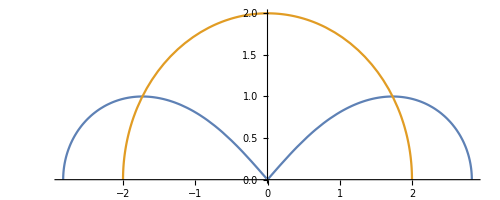

```mathematica
PolarPlot[{F[θ],G[θ]},{θ,0,π}]
```

## Problem 7:

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[θ_]:=5+3*Sin[θ];
G[θ_] := 5+3*Sin[θ];
```

```mathematica
Eliminate[{Tan[θ]==x/y,r^2==x^2+y^2,r==5+3*Sin[θ],r==5+3*Sin[θ]},{θ,r}]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

x^8+x^6 (-68+4 y^2)+x^2 y^2 (800-168 y^2+4 y^4)+x^4 (256-186 y^2+6 y^4)==y^4 (-625+50 y^2-y^4)&&y≠0

```mathematica
Solve[x^8+x^6 (-68+4 y^2)+x^2 y^2 (800-168 y^2+4 y^4)+x^4 (256-186 y^2+6 y^4)==y^4 (-625+50 y^2-y^4)&&y≠0,y]
```

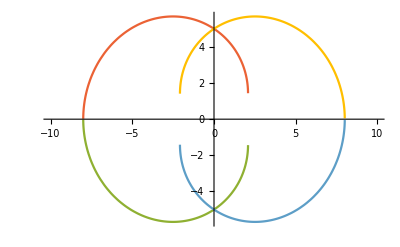

```mathematica
Plot[{y=-(√(25-5 √(25-12 x)-6 x-2 x^2))/(√2),y=(√(25-5 √(25-12 x)-6 x-2 x^2))/(√2),y=-√(25/2+5/2 √(25-12 x)-3 x-x^2),y=√(25/2+5/2 √(25-12 x)-3 x-x^2),y=-(√(25+6 x-2 x^2-5 √(25+12 x)))/(√2),y=(√(25+6 x-2 x^2-5 √(25+12 x)))/(√2),y=-√(25/2+3 x-x^2+5/2 √(25+12 x)),y=√(25/2+3 x-x^2+5/2 √(25+12 x))},{x,-10,10}]
```

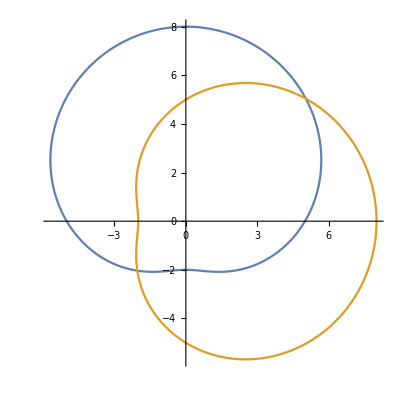

```mathematica
PolarPlot[{F[θ],G[θ]},{θ,0,2π}]
```

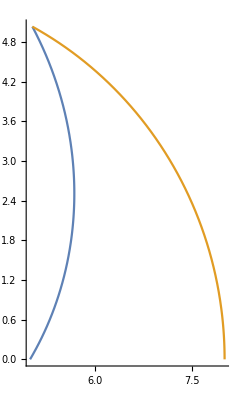

```mathematica
PolarPlot[{F[θ],G[θ]},{θ,0,π/4}]
```

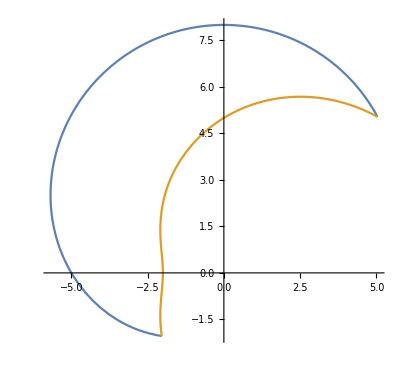

```mathematica
PolarPlot[{F[θ],G[θ]},{θ,π/4,(5π)/4}]
```

```mathematica
Solve[F[θ]==G[θ],θ]
```

```mathematica
(* θ = π/4
θ = 5π/4 *)
```

```mathematica
1/2*∫_(π/4)^(5 π/4) ((F[θ])^2)ⅆθ
```

1/2 (30 √2+(59 π)/2)